```mathematica
(* Elementary Programming *)

f[x_]:=If[x>0,N[Sin[x]],0]
```

```mathematica
f[π/2]
```

1.

```mathematica
g[n_]:=If[Mod[n,2]==0,n/2,3n+1]
```

```mathematica
g[#]&/@{34,33,98,9}
```

{17,100,49,28}

```mathematica
h[x_]:=If[x>0,1,
If[x<0,-1,0]
]
```

```mathematica
h[#]&/@{2,3,-4,5,0}
```

{1,1,-1,1,0}

```mathematica
Do[
Print[{i,i^3}],{i,1,5}
]
```

{1,1}

{2,8}

{3,27}

{4,64}

{5,125}

```mathematica
Timing[
fibonnaciNumbers={0,1};
Do[
a=fibonnaciNumbers[[-1]];
b=fibonnaciNumbers[[-2]];
AppendTo[fibonnaciNumbers,a+b],
{i,1,29}
]
]
fibonnaciNumbers
```

{0.,Null}

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

```mathematica
k=5;
While[
k>1,k=g[k];
Print[k]
]
```

16

8

4

2

1

```mathematica
k=97;
While[k>1,k=g[k];
Print[k]
]
```

292

146

73

220

110

55

166

83

250

125

376

188

94

47

142

71

214

107

322

161

484

242

121

364

182

91

274

137

412

206

103

310

155

466

233

700

350

175

526

263

790

395

1186

593

1780

890

445

1336

668

334

167

502

251

754

377

1132

566

283

850

425

1276

638

319

958

479

1438

719

2158

1079

3238

1619

4858

2429

7288

3644

1822

911

2734

1367

4102

2051

6154

3077

9232

4616

2308

1154

577

1732

866

433

1300

650

325

976

488

244

122

61

184

92

46

23

70

35

106

53

160

80

40

20

10

5

16

8

4

2

1

```mathematica
k=197234;
m[x_]:=If[Mod[x,2]==0,x/2,x+1];
While[k>1,k=m[k];
Print[k]
]
```

98617

98618

49309

49310

24655

24656

12328

6164

3082

1541

1542

771

772

386

193

194

97

98

49

50

25

26

13

14

7

8

4

2

1

```mathematica
(* using modules *)

(* find the nearest prime to n *)

nearprimes[n_]:=(
bigger=n;
While[PrimeQ[bigger]==False,bigger++];

smaller=n;
While[PrimeQ[smaller]==False,smaller--];

{smaller,bigger}
)
```

```mathematica
nearprimes[411]
```

{409,419}

```mathematica
nearprimes1[n_]:=Module[
{bigger,smaller},
bigger=n;
While[PrimeQ[bigger]==False,bigger++];
smaller=n;
While[PrimeQ[smaller]==False,smaller--];
{smaller,bigger}
]
```

```mathematica
{bigger,smaller}
```

{419,409}

```mathematica
nearprimes1[34]
```

{31,37}

```mathematica
{smaller,bigger}
```

{409,419}

```mathematica
(* sieve of eratosthenes *)

sieve[n_]:=Module[
{net,j},
(* initialize the sieve *)

net=Range[n];

(* for each k from 2 to n/2 see if it is "crossed out." 
If not,cross out all of its multiples *)

Do[
If[
(* see if k has been crossed out *)
net[[k]]≠0,
(* cross out all its multiples *)
j=2 k;
While[j≤n,net[[j]]=0;j+=k]
],
{k,2,n/2}
];
(* sort and drop 0 and 1 *)
Drop[Union[net],2]
]

collatz[n_]:=Module[
{k=n,orbit={n}},
g[x_]:=If[Mod[x,2]==0,x/2,3x+1];
While[
k>1,AppendTo[orbit,k=g[k]]
];
orbit
]
```

```mathematica
collatz[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

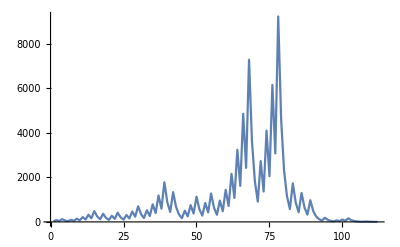

```mathematica
ListPlot[collatz[27],Joined->True,PlotRange->All]
```

```mathematica
collatzStoppingTime[n_]:=Module[
{k=n,count=0},
While[k>1,k=g[k];count++];
count
]
```

```mathematica
collatzStoppingTime[29]
```

18